```mathematica
PM={IdentityMatrix[2],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[μ_]:=PM⟦μ+1⟧
X[μ_,ν_]:=KroneckerProduct[PM⟦μ+1⟧,PM⟦ν+1⟧]
X[μ_,ν_,ρ_]:=KroneckerProduct[PM⟦μ+1⟧,PM⟦ν+1⟧,PM⟦ρ+1⟧]
zero2=ConstantArray[0,{2,2}];zero4=ConstantArray[0,{4,4}];
```

## Momentum Space

## The Hamiltonian

```mathematica
(*Minimal Model: C_Mz = 2 TCI with broken Mz but preserved Inversion & TRS symmetry*)
```

```mathematica
HBulk[k_]:= ArrayFlatten@{{(1+Cos[k[[1]]]+Cos[k[[2]]])X[0,1]+Sin[k[[1]]]X[0,2]+Sin[k[[2]]]X[0,3],zero4},{zero4,-(1+Cos[k[[1]]]+Cos[k[[2]]])X[0,1]+Sin[k[[1]]]X[0,2]+Sin[k[[2]]]X[0,3]}}
dimH = Length@HBulk[{0,0,0}];
```

```mathematica
(*Plot3D[Sort@Eigenvalues@HBulk[{kx,ky}],{kx,0,2Pi},{ky,0,2Pi}]*)
```

## Symmetries

```mathematica
TRS=I X[1,0,2];
```

```mathematica
Norm[TRS.Conjugate[HBulk[{1.,2.}].Inverse[TRS]]-HBulk[-{1.,2.}]]
```

0.

```mathematica
Mz=I X[3,0,0];
```

```mathematica
Norm[Mz.HBulk[{1.,2.}].Inverse[Mz]-HBulk[{1.,2.}]]
```

0.

```mathematica
C2=I X[0,0,1];
```

```mathematica
Norm[C2.HBulk[{1.,2.}].Inverse[C2]-HBulk[-{1.,2.}]]
```

0.

```mathematica
Ch=X[1,0,1];
```

```mathematica
Norm[Ch.HBulk[{1.,2.}].Inverse[Ch]+HBulk[{1.,2.}]]
```

0.

```mathematica
Inv=C2.Mz;
```

```mathematica
Norm[Inv.HBulk[{1.,2.}].Inverse[Inv]-HBulk[-{1.,2.}]]
```

0.

## Breaking Mz

```mathematica
MatAllowed=Table[Norm[TRS.Conjugate[X[i,j,k]].Inverse[TRS]-X[i,j,k]]+Norm[Ch.X[i,j,k].Inverse[Ch]+X[i,j,k]]+Norm[Inv.X[i,j,k].Inverse[Inv]-X[i,j,k]],{i,0,3},{j,0,3},{k,0,3}];
```

```mathematica
HBulkNew[{kx_,ky_}]=HBulk[{kx,ky}]+Sum[Which[MatAllowed[[a+1,b+1,c+1]]==0,(RandomReal[0.5]-0.25)X[a,b,c],True,ConstantArray[0,{8,8}]],{a,0,3},{b,0,3},{c,0,3}];
```

```mathematica
filling=1/2;
```

```mathematica
(*Plot3D[Sort@Eigenvalues@HBulkNew[{kx,ky}],{kx,0,2Pi},{ky,0,2Pi}]*)
```

## Symmetries for broken MZ

```mathematica
Norm[TRS.Conjugate[HBulkNew[{1.,2.}].Inverse[TRS]]-HBulkNew[-{1.,2.}]]
```

0.

```mathematica
Norm[Mz.HBulkNew[{1.,2.}].Inverse[Mz]-HBulkNew[{1.,2.}]]
```

0.516591

```mathematica
Norm[C2.HBulkNew[{1.,2.}].Inverse[C2]-HBulkNew[-{1.,2.}]]
```

0.516591

```mathematica
Norm[Ch.HBulkNew[{1.,2.}].Inverse[Ch]+HBulkNew[{1.,2.}]]
```

0.

```mathematica
Norm[Inv.HBulkNew[{1.,2.}].Inverse[Inv]-HBulkNew[-{1.,2.}]]
```

0.

## Real Space

## Discrete Fourier Transform

```mathematica
a1={1,0};a2={0,1};
```

```mathematica
b1 = 2Pi a1;b2= 2Pi a2;
```

```mathematica
LBZ=3;
```

```mathematica
BZ=Flatten[Table[i/LBZ*b1+j/LBZ*b2,{i,0,LBZ-1},{j,0,LBZ-1}],1];
```

```mathematica
H[k_]:=N@HBulkNew[k]
```

```mathematica
HonSite =1/LBZ^2*Sum[H[{k[[1]],k[[2]]}],{k,BZ}];
Hhopa1 =1/LBZ^2*Sum[Exp[I k.a1]*H[{k[[1]],k[[2]]}],{k,BZ}];
Hhopa2 =1/LBZ^2*Sum[Exp[I k.a2]*H[{k[[1]],k[[2]]}],{k,BZ}];
```

```mathematica
L=24;lp=Ceiling[L/2];
```

```mathematica
slabx=True;slaby=True;
loc[k_]:={Mod[k,L]+L*Boole[Mod[k,L]==0],1+(k-Mod[k,L]-L*Boole[Mod[k,L]==0])/L}
up[k_]:= Boole[!slaby]*Boole[k-L ≤ 0] * (k + L * (L-1)) + Boole[k-L>0]*(k-L)
right[k_]:= Boole[!slabx]*Boole[Mod[k,L]==0]*(k-L+1) + Boole[Mod[k,L] ≠ 0] * (k +1)
```

```mathematica
HSlab =SparseArray@Block[{HonS=HonSite,Hright=Hhopa1,Hup=Hhopa2},ArrayFlatten@Table[Which[i==j,HonS,j==right[i], Hright,i==right[j], ConjugateTranspose[Hright],j==up[i],Hup,i==up[j],ConjugateTranspose[Hup],
True,ConstantArray[0,{dimH,dimH}]],{i,L^2},{j,L^2}]];
```

## Evaluate

```mathematica
pdat=Sort@Eigenvalues[HSlab,-32];
```

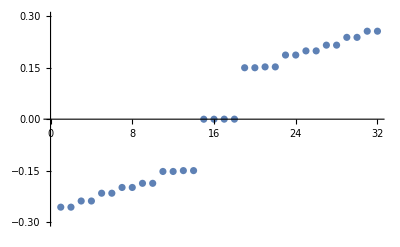

```mathematica
ListPlot[pdat,PlotRange->{-.3,.3}]
```